### a)

{{x→0,y→0}}

{{y→-(3 x)/4}}

{{x→0,y→0}}

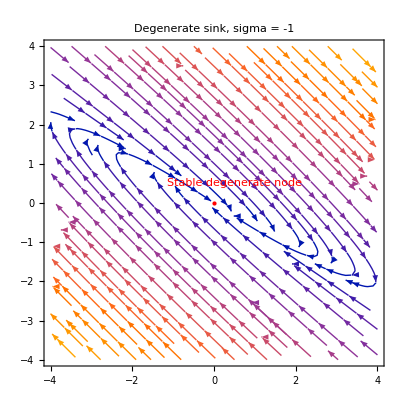

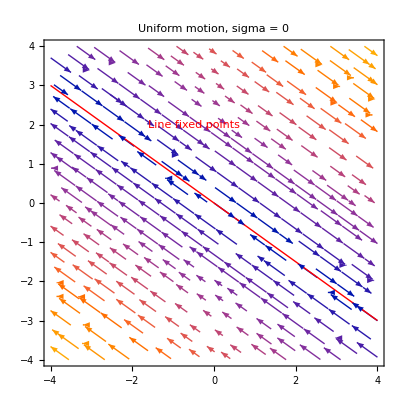

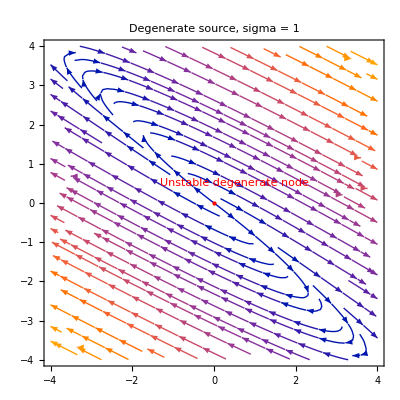

```mathematica
sigmaOne = -1;
Solve[(sigmaOne+3)*x+4*y==0&&-(9/4)*x+(sigmaOne-3)*y==0,{x,y}]

sigmaTwo = 0;
Solve[(sigmaTwo+3)*x+4*y==0&&-(9/4)*x+(sigmaTwo-3)*y==0,{x,y}]

sigmaThree= 1;
Solve[(sigmaThree+3)*x+4*y==0&&-(9/4)*x+(sigmaThree-3)*y==0,{x,y}]


plot1 =StreamPlot[{(σ+ 3)x + 4y, -(9/4)x + (σ-3)y} /. {σ -> -1},{x,-4,4},{y,-4,4}, PlotLabel-> "Degenerate sink, sigma = -1",Epilog->{Red,PointSize[Medium],Point[{0,0}],Text["Stable degenerate node",{0.5,0.5}]}];
plot2 = StreamPlot[{(σ+ 3)x + 4y, -(9/4)x + (σ-3)y} /. {σ -> 0},{x,-4,4},{y,-4,4}, PlotLabel-> "Uniform motion, sigma = 0",Epilog->{Red,PointSize[Medium],Line[{{-4,3},{4,-3}}],Text["Line fixed points",{-0.5,2}]}];
plot3 = StreamPlot[{(σ+ 3)x + 4y, -(9/4)x + (σ-3)y} /. {σ -> 1},{x,-4,4},{y,-4,4}, PlotLabel-> "Degenerate source, sigma = 1",Epilog->{Red,PointSize[Medium],Point[{0,0}],Text["Unstable degenerate node",{0.5,0.5}]}];
Show[plot1]
Show[plot2]
Show[plot3]
```

### b),c),d)

Normalize the eigenvectors and put x-component positive (-1*[x,y]) for d)

```mathematica
m = {{sigma+3,4},{-9/4,sigma-3}};
Eigenvalues[m]
Eigenvectors[m]
Inverse[m]
```

{sigma,sigma}

{{-4/3,1},{0,0}}

{{(-3+sigma)/sigma^2,-4/sigma^2},{9/(4 sigma^2),(3+sigma)/sigma^2}}

### e)

The value of sigma for which M_sigma is singular is 0 since dividing by zero gives a singularity and inverse of M_sigma doesn’t exist for this value of sigma.

{sigma,sigma}

{{-4/3,1},{0,0}}

{{(-3+sigma)/sigma^2,-4/sigma^2},{9/(4 sigma^2),(3+sigma)/sigma^2}}

{{-c d+sigma,d^2},{-c^2,c d+sigma}}

{sigma,sigma}

{sigma/(√2 Abs[sigma]),sigma/(√2 Abs[sigma])}

### f)

```mathematica
Solve[-c*d==3&&d^2==4&&-c^2==-9/4&&c*d==-3,{c,d}]
```

{{c→-3/2,d→2},{c→3/2,d→-2}}

### g)

```mathematica
M = {{sigma-c*d,d^2},{-c^2,sigma+c*d}};
V = Eigenvalues[M]
```

### h)

```mathematica
sigma0 = 0;
Mv = {{sigma0-c*d,d^2},{-c^2,sigma0+c*d}};
Eigenvectors[Mv];
v= {d/c,1};
v = Normalize[v]
```

{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}

{{-c d,d^2},{-c^2,c d}}

{{d/c,1},{0,0}}